```mathematica
(*Final*)
```

```mathematica
(* -------------- Math functions ---------------*)

Rotz4[θ_]:=({{Cos[θ], -Sin[θ], 0, 0}, {Sin[θ], Cos[θ], 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}})
Rotz[θ_]:=({{Cos[θ], -Sin[θ], 0}, {Sin[θ], Cos[θ], 0}, {0, 0, 1}})
Vec3[v1_,v2_,v3_]:={{v1},{v2},{v3}}
Trans4[x_,y_]:=({{1, 0, 0, x}, {0, 1, 0, y}, {0, 0, 1, 0}, {0, 0, 0, 1}})
NewT4[x_,y_,θ_]:=Trans4[x,y].Rotz4[θ]
Zeros[dim1_,dim2_]:=Table[0,{i,1,dim1},{j,1,dim2}]
MF[T_]:=MatrixForm[T]

(* Skew funcs *)
Hat[ω_]:=({{0, -ω[[3,1]], ω[[2,1]]}, {ω[[3,1]], 0, -ω[[1,1]]}, {-ω[[2,1]], ω[[1,1]], 0}})
Unhat[ω_]:={{ω[[3,2]]},{ω[[1,3]]},{ω[[2,1]]}}

(* generalized hat: g -> twist *)
Genhat2[ω_,v_]:=ArrayFlatten[({{Hat[ω], v}, {Zeros[1,3], 0}})]
Genhat[S_]:=Module[{ω,v},
ω=S[[1;;3,1;;1]];
v=S[[4;;6,1;;1]];
Genhat2[ω,v]
]
GenUnhat[T_]:=Join[Unhat[T[[1;;3,1;;3]]],T[[1;;3,4;;4]]]
AdT[T_]:=Module[{R,p},
R=T[[1;;3,1;;3]];
p=T[[1;;3,4;;4]];
ArrayFlatten[({{R, Zeros[3,3]}, {Hat[p].R, R}})]
]
InvT[T_]:=Module[{R,p},
R=T[[1;;3,1;;3]];
p=T[[1;;3,4;;4]];
ArrayFlatten[({{Transpose[R], -Transpose[R].p}, {Zeros[1,3], 1}})]
]
(* Math funcs*)
(*return the distance between p1 and p2*)
CalcDist[x1_,y1_,x2_,y2_]:=Sqrt[(x2-x1)^2+(y2-y1)^2];

(* return the angle between (pb,p0) and (pb,p1) *)
CosLaw[x0_,y0_,x1_,y1_,xb_,yb_]:=Module[
{a,b,c,costheta},
a=CalcDist[xb,yb,x0,y0];
       b=CalcDist[xb,yb,x1,y1];
c=CalcDist[x0,y0,x1,y1];
costheta=(a^2+b^2-c^2)/(2*a*b);
ArcCos[costheta]
];

myArcTan[x0_,y0_,x1_,y1_]:=ArcTan[y1-y0,x1-x0];
myPiToPi[theta_]:=Which[theta>Pi,theta-2*Pi,theta<-Pi,theta+2*Pi,True,theta];

(*Check if the projection of pb=(xb,yb) is in the line of p0~p1*)
isInLine[x0_,y0_,x1_,y1_,xb_,yb_]:=Module[
{dx,dy,innerproduct},
dx=x1-x0;
dy=y1-y0;
innerproduct=(xb-x0)*dx+(yb-y0)*dy;
0≤innerproduct&&innerproduct≤dx*dx+dy*dy
];

(* Mathematica expression related funcs *)
setTimeVars[vs_]:=Table[vs[[i]][t],{i,1,Length[vs]}];
TurnToEq[list1_,list2_]:=Module[{tmp},
tmp=Flatten[list1];Table[tmp[[i]]==list2[[i]],{i,1,Length[tmp]}]];
(* ----------- Math funcs ends here. ---------------;-------------- Below are the main program. --------------*)
```

```mathematica
(* ---------------- vars ----------------*)
nVars=0;
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
qs={};
qsvars={};
qsInit={};
dqsInit={};
(* ------------ objects ----------------- *)
nObjects=0;
objNames={};
(* Properties *)
l=l1=l2=l3=1;
w=w1=w2=w3=0.25;
masses={};
inertias={};
lens={l1,l2,l3};
widths={w1,w2,w3};
g=9.8;
(* Transformation matrices *)
Ts={};
```

```mathematica
(* ------------ Create objects ----------------- *)
CreateTriangle[l_,objqsinit_,objdqsinit_]:=Module[{},
(*Properties*)
objNames=Append[objNames,"Triangle"];
mass=1;
inertia=1;
(*Vars*)
nDOF=3;
objqsvars=Table[Symbol["$q"<>ToString@i],{i,nVars+1,nVars+nDOF}];
objqs=setTimeVars[objqsvars];(* x -> x[t] *)
x=objqsvars[[1]];
y=objqsvars[[2]];
θ=objqsvars[[3]];
(*Geometry*)
Tw=Trans4[0,0];
T1=Tw.Trans4[x[t],y[t]].Rotz4[θ[t]]//Simplify;
p1End1=T1.Transpose[{{0,l/Sqrt[3],0,1}}]//Simplify;
p1End2=T1.Transpose[{{l/2,-l/(2*Sqrt[3]),0,1}}]//Simplify;
p1End3=T1.Transpose[{{-l/2,-l/(2*Sqrt[3]),0,1}}]//Simplify;
p1Ends={p1End1,p1End2,p1End3};
(*Output/Update*)
nObjects=nObjects+1;
nVars=nVars+nDOF;
qs=Join[qs,objqs];
qsvars=Join[qsvars,objqsvars];
Ts=Append[Ts,T1];
masses=Append[masses,mass];
inertias=Append[inertias,inertia];
qsInit=Join[qsInit,objqsinit];
dqsInit=Join[dqsInit,objdqsinit];
(*Return*)
T1
];
(* Triangle *)
t1len=1;
t1qsInit={0,0,0};
t1dqsInit={0,0,0};

gTriangle1=CreateTriangle[t1len,t1qsInit,t1dqsInit];
```

```mathematica
(* Prepare *)
dqs=D[qs,t];
ddqs=D[dqs,t];
qsInit=ConstantArray[0,nVars];
dqsInit=ConstantArray[0,nVars];
```

```mathematica
(* --------------- Left side of EL eqs -------------- *)
(* Body generalized mass, composed of Inertia Tensor and Mass Matrix *)
getGb[j_,m_]:=ArrayFlatten[({{DiagonalMatrix[{j,j,j}], Zeros[3,3]}, {Zeros[3,3], DiagonalMatrix[{m,m,m}]}})]
Gbs=Table[getGb[inertias[[i]],masses[[i]]],{i,1,nObjects}]//Simplify;
(* Body screw axis *)
Vbs=Table[GenUnhat[InvT[Ts[[i]]].D[Ts[[i]],t]],{i,1,nObjects}]//Simplify;
(* Lagrange Equations: Kinetic and Potential Energy *)
GetKE[Gb_,Vb_]:=(1/2*Transpose[Vb].Gb.Vb)[[1,1]];
GetPE[m_,T_]:=m*g*T[[2,4]];
KEs=Table[GetKE[Gbs[[i]],Vbs[[i]]],{i,1,nObjects}]//Simplify;
PEs=Table[GetPE[masses[[i]],Ts[[i]]],{i,1,nObjects}]//Simplify;
Lag=Total[Join[KEs,-PEs]]//Simplify;
(* Left side of Euler-Lagrange Equations*)
ELeqsLeft=D[D[Lag,{dqs}],t]-D[Lag,{qs}]//Simplify;
```

```mathematica
(* --------------- Right side of EL eqs -------------- *)
(* Constraints *)
(*
conslink1P1x=p1Ends[[1]][[2,1]];(* y=0 *)
conslink1P1y=p1Ends[[2]][[2,1]];(* y=0 *)
*)
cons={}//Simplify;
nCons=Length[cons];
If[nCons>0,
(λs=Transpose[{Table[Symbol["$λ"<>ToString@i],{i,nCons}]}];
consgrad=Transpose[Grad[cons,qs]]; (* Grad[2,5]->Mat(2,5),Transpose->(5,2)*)
consddt=D[D[cons,t],t]//Simplify)];
```

```mathematica
(* External forces *)
externalForces=ConstantArray[0,nVars];
```

```mathematica
(* ----------------------------- *)
(* Solve *)
If[nCons>0,(* with constraints *)
(EulerLagEqs=Thread[ELeqsLeft==Flatten[consgrad.λs]+externalForces]//Simplify;
consddtEqs=TurnToEq[consddt,ConstantArray[0,nCons]];
EQ=Solve[Join[EulerLagEqs,consddtEqs],Join[ddqs,Flatten[λs]]]),
(* No constraint *)
EulerLagEqs=TurnToEq[ELeqsLeft,externalForces]//Simplify;
EQ=Solve[EulerLagEqs,ddqs]];
```

```mathematica
(* Preprae for NDSolve *)
SetUpImpacts
ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];
q0Solve=TurnToEq[qs/.t->0,qsInit];
dq0Solve=TurnToEq[dqs/.t->0,dqsInit];
```

```mathematica
(* NDsolve *)
timeend=2;

ifprint=True;
impactDetectionError=0.01;
intergrationMaxStepSize=0.01;

{end,data,bounces}=BouncingBall[qsInit,dqsInit];

(*
timeend=10;
ddqSolve=TurnToEq[ddqs,EQ[[1,;;,2]]];
q0Solve=TurnToEq[qs/.t->0,qsInit];
dq0Solve=TurnToEq[dqs/.t->0,dqsInit];
sim=NDSolve[{ddqSolve,q0Solve,dq0Solve},qsvars,{t,0,timeend},Method->{"EquationSimplification"->"Residual"}];*)
```

time=2.

Before reflection, q={{0.,-19.6,0.},{0.,-19.6,0.}}

After reflection{0.,-19.6,0.}

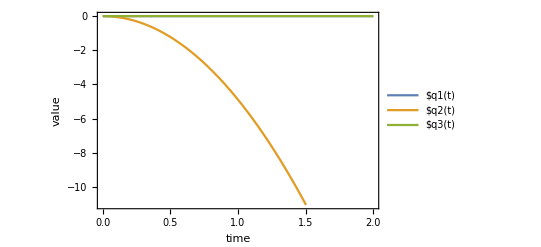

```mathematica
(* Plot *)

qsHist=Piecewise["qhist"/.data][[1,1,1]];
Show[Plot[Evaluate[qsHist],{t,0,end},PlotLegends->qs,
	PlotRange->Automatic,Frame->True,FrameLabel->{"time","value"}]]
```

```mathematica
plotRect[T_,k_]:=Module[{p0,p1,p2,p3,p4,p,pw,l,w},
l=lens[[k]];
w=widths[[k]];
p0={-w/2,l/2,0,1};
p1={w/2,l/2,0,1};
p2={w/2,-l/2,0,1};
p3={-w/2,-l/2,0,1};
p4={-w/2,l/2,0,1};
p={p0,p1,p2,p3,p4};
pw=(T.Transpose[p])[[1;;2,;;]];
Table[Line[{pw[[1;;2,i]],pw[[1;;2,i+1]]}],{i,1,4}](* {Line1,Line2,...]}*)
]

plotTriangle[pEnds_]:=Module[{p1,p2,p3,pw},
p1=pEnds[[1]];p2=pEnds[[2]];p3=pEnds[[3]];
pw={p1,p2,p3,p1};
Table[Line[{pw[[i,1;;2,1]],pw[[i+1,1;;2,1]]}],{i,1,3}]
]
links={plotTriangle[p1Ends]};
```

```mathematica
(* Animate *)
(*linksCoords[i_]:=(links[[i]]/.sim)[[1]];*)
linksCoords[j_]:=links[[j]]/.Table[qs[[i]]->qsHist[[i]],{i,1,nVars}];
LinksForAnimation[tt_]:=(Table[linksCoords[i],{i,1,Length[links]}])/.t->tt;
Animate[Show[
{Graphics[LinksForAnimation[t][[1]]]
},PlotRange-> {{-3,3},{-30,3}},Frame-> True],{t,0,timeend}]
```